# MATH7501 Practical 3, Semester 1-2021

## Topic: Matrices and Sets

Author:  Aminath Shausan
Date: 12-03-2021

## Pre-Tutorial Activity

Students must have familiarised themselves with units 1 and 2 contents (Matrices, Sets) of the reading materials for MATH7501

## Resources

https://reference.wolfram.com/language/guide/OperationsOnSets.html

## Q 1. Cardinality, Member, Subset and Powerset of a Set

Suppose A = {1, 2, {3}}.  Determine if the following statements are true or false.

```mathematica
Clear[A]
```

```mathematica
A = {1, 2, {3}}
```

{1,2,{3}}

(a) |2^A| = 2^(|A|) . Use may use Length[ ]  function to compute cardinality (total number of elements) of a set and Subsets[ ] function to compute all subsets of A (which is the powerset )

```mathematica
Subsets[A]
Length[Subsets[A]] 
Length[Subsets[A]] == 2^Length[A]
```

{{},{1},{2},{{3}},{1,2},{1,{3}},{2,{3}},{1,2,{3}}}

8

True

(b) {3} ⊂ A.  (Use SubsetQ[ ]  function)

```mathematica
SubsetQ[A, {{3}}]
SubsetQ[A, {3}]
```

True

False

(c) {1,2} ∈ 2^A.  (Use MemberQ[ ]  function)

```mathematica
MemberQ[Subsets[A],{1,2}]
```

True

```mathematica
Clear[A]
```

## Q 2. Set Intersection, Union and Complement

Suppose A = {k ∈ ℕ | k is divisible by 2} and B = {k ∈ ℕ | k+1 is divisible by 2}
(a) what is the set A ∩ B (ie. the common elements in both A and B)

A = {k ∈ ℕ | k = 2 n, for integer n}, B  = {k ∈ ℕ | k = 2 n - 1, for integer n}. For n ∈ ℕ, 
A = {2, 4, 6, 8, 10 ....}
B =  {1, 3, 5, 7, 9 ....}
So A ∩ B = { }
If considering the following finite sets, you can use Intersection[ ] function to compute intersection of A and B

```mathematica
A = {2,4,6,8,10,12,14,16,18,20};
B = {1,3,5,7,9,11,13,15,17,19};
```

```mathematica
Intersection[A,B]
```

{}

(b) what is the set  ℕ\(A ∪ B)

A∪B is the set which contains all elements in A and B. So 
A∪B ={1, 2, 3, 4, 5, 6, 7, 8, 9, 10, ...} = ℕ. Thus, the complement of A∪B in ℕ is
ℕ\(A ∪ B)  = { }
Considering the finite sets for A and B you can use the Union[ ] and Complement[ ] functions to compute union of sets and complement of a set.

```mathematica
Nat = Table[n, {n, 20} ]
```

```mathematica
{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}
```

```mathematica
AunionB = Union[A,B]
Complement[Nat, AunionB]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

{}

(c) If Cr= {k ∈ ℕ| k ≲ r} , determine |A ∩ C|, for r = 10, 20, using simulation. 
The function lenAintC[ ] below computes this.

```mathematica
ClearAll[r, Cr, A,B]
```

```mathematica
lenAintC[r_]:= Module[{A,Cr, AinterC}, 
                                                 Cr= Table[k,{k,r}];
                                                  A= Select[Cr,EvenQ];
                                                  AinterC = Intersection[A, Cr];
                                                  Length[AinterC]
                                                ]
```

```mathematica
lenAintC[20]
```

10

## Q 3. Estimating Least Square Regression Coefficients

Consider matrix A and vector y below.

```mathematica
A = ({{1, 3.4}, {1, 3.7}, {1, 5.9}, {1, 6.9}, {1, 9.1}});y=({{2.1}, {3.7}, {5.8}, {8.6}, {6.4}});
```

(a) Generate a million random entries in [0, 5] ×[0,5] for β = [β_0, β_1]ᵀ, and estimate β which minimises ||Aβ - y||.
The function lineFit[ ] below performs this simulation.

```mathematica
lineFit[nrun_]:= Module[{beta, error, norm, n=nrun, est},
beta = RandomReal[{0,5},{2,n}];
norm =ConstantArray[0,n];
For[i=1, i< n+1,i++, 
error =A.beta[[All,i]]-y;
norm [[i]]= Norm[error];
(*Print[error];*)  (* comment*)
];
          (*Print[norm];*)
	min = Min[norm]; Print[min];
	indx = Position[norm,min][[1,1]]; Print[indx];
	(*Print[beta];*)
         beta[[All,indx]]
]
```

```mathematica
lineFit[100000]
```

3.1679

4989

{0.520032,0.82554}

So the estimates for β is about (0.520032,0.82554)ᵀ using 100,000 runs.

(b) Find the best β using β = (AᵀA)^-1 Aᵀy

```mathematica
Inverse[Aᵀ.A].Aᵀ.y//MatrixForm
```

(0.54307
0.823609)

(c) Plot the points and line of best fit

```mathematica
xx  = A[[All,2]]; 
yy = y[[All,1]]; (* (xx, yy) are the data points*)
```

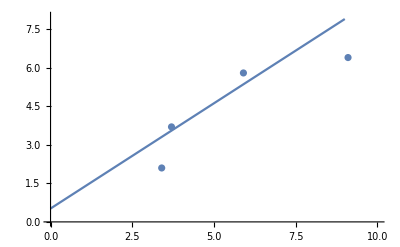

```mathematica
data = ListPlot[Thread[{xx,yy}], PlotRange->{{0,10},{0,8}}]; (*this plots the data*)
line = Plot[0.52+0.82 x,{x,0,9}];   (*this plots the line of best fit using the estimates for β*)Show[data,line]
```

## Q 4. Binomial Coefficient

(a) Find all solutions of x_1+x_2+x_3= 2
First find the number of solutions using

(n+k-1
k), with n=3, k=2. You may use Binomial[] functionto compute this.

```mathematica
n =3
k=2
```

3

2

```mathematica
Binomial[n+k-1,2]
```

6

Find all solutions